```mathematica
(* Create vertices of a sevenfold tiling. Furthermore check that no vertices are duplicated. *)
tiling7=RunThrough["/homes/tjakobi/PhD_Work/radialprojection/higher_cyclo --hepta 30 0",Null];
{Length[tiling7],Length[Union[tiling7]]}
```

{11817,11817}

```mathematica
(* The seventh root of unity, used for mapping the vertices to physical space. *)
z7:=Exp[I*2*Pi/7];
```

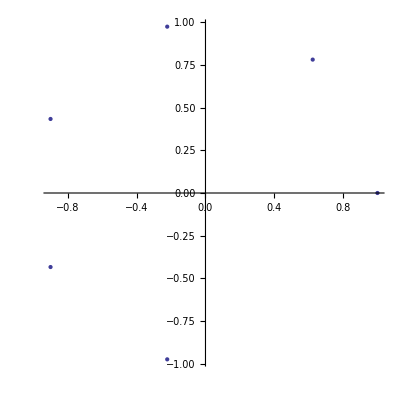

```mathematica
ListPlot[Map[{Re[#],Im[#]}&,Table[z7^k,{k,0,5}]],AspectRatio->1.0]
```

```mathematica
(* The transformation matrix to physical space. *)
transMtx7=Transpose[Map[{Re[#],Im[#]}&,Table[z7^k,{k,0,5}]]];
transMtx7//MatrixForm
```

(1 | Sin[(3 π)/14] | -Sin[π/14] | -Cos[π/7] | -Cos[π/7] | -Sin[π/14]
0 | Cos[(3 π)/14] | Cos[π/14] | Sin[π/7] | -Sin[π/7] | -Cos[π/14])

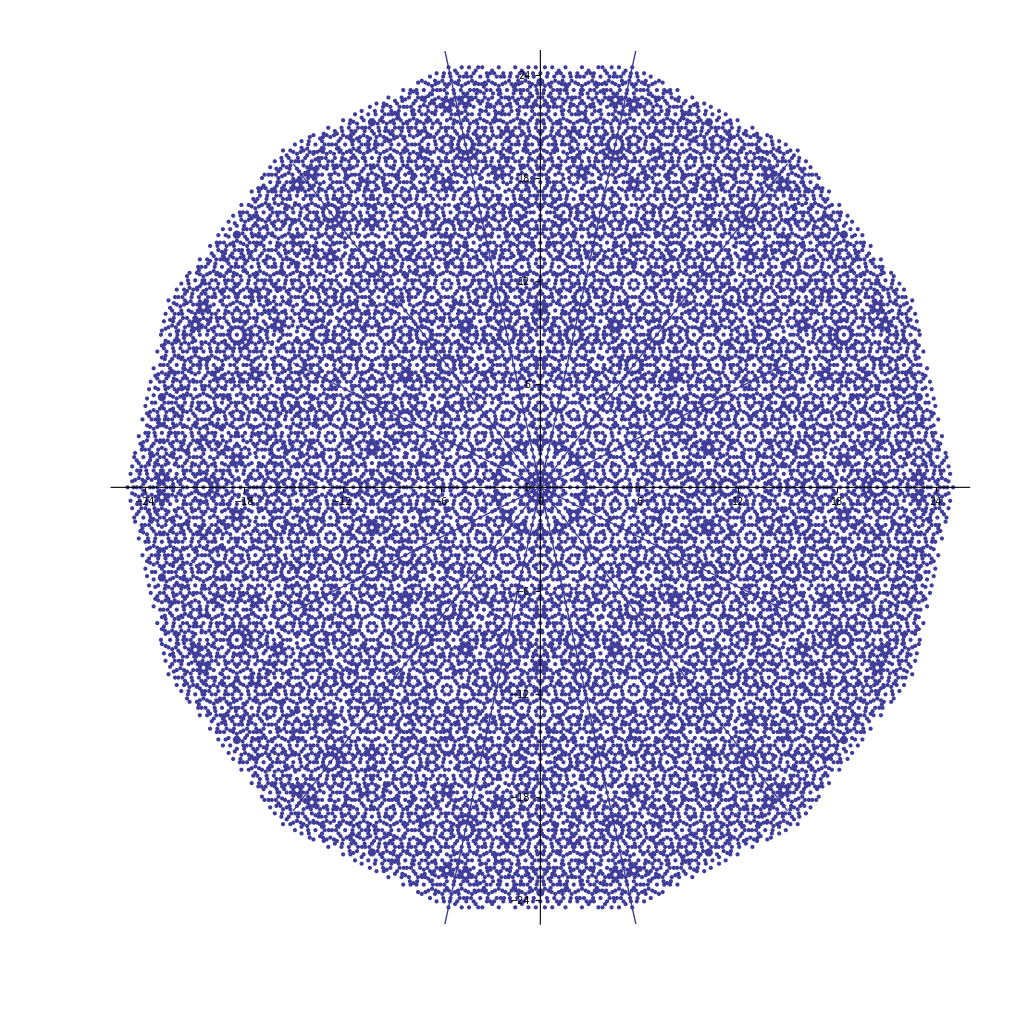

```mathematica
(* Plot the tiling vertices. *)
Show[ListPlot[Map[transMtx7.#&,tiling7],AspectRatio->1.0],
Sequence[Table[Plot[Tan[k*Pi/7]*t,{t,-15,15}],{k,1,6}]]]
```

```mathematica
(* Import external envelope data created from a larger patch. *)
envelopeData[Hepta]=ReadDoubleData["/homes/tjakobi/PhD_Work/radialprojection/datafiles/hepta.env"];
envelopeFct[Hepta]=Interpolation[transformEnvData[Hepta,{4.0,0.02}]];
```

```mathematica
(* Distribution of the radial projection looks very much like the octagonal case. *)
Plot[envelopeFct[Hepta][t],{t,0,4}]
```

```mathematica
tiling11=RunThrough["/homes/tjakobi/PhD_Work/radialprojection/higher_cyclo --eleven 3 1",Null];
{Length[tiling11],Length[Union[tiling11]]}
```

```mathematica
(* The eleventh root of unity. *)
z11:=Exp[I*2*Pi/11];
```

```mathematica
transMtx11=Transpose[Map[{Re[#],Im[#]}&,Table[z11^k,{k,0,9}]]];
transMtx11//MatrixForm
```

```mathematica
Show[ListPlot[Map[transMtx11.#&,tiling11],AspectRatio->1.0,PlotStyle->{PointSize[0.006]}],
Sequence[Table[Plot[Tan[k*Pi/11]*t,{t,-15,15}],{k,1,10}]],
ListPlot[{Function[x,{Cos[x],Sin[x]}][2*Pi/11]},PlotStyle->Red]]
```

```mathematica
angles11=Map[N[ArcTan[Part[#,1],Part[#,2]]]&,Map[transMtx11.#&,tiling11]];
```

```mathematica
{Length[angles11],Length[Union[angles11]]}
```

```mathematica
Histogram[Function[x,Drop[x-RotateLeft[x],-1]][Sort[angles11,Greater]]]
```

```mathematica
mini11[t_]=MinimalPolynomial[2*Cos[2*Pi/11],t]
```

```mathematica
multFunc[poly_]:=Expand[poly*t];
reduceFunc[poly_]:=Expand[poly/.{t^5->-t^4+4*t^3+3*t^2-3*t-1}];
```

```mathematica
Map[Nest[reduceFunc[multFunc[#]]&,t^4,#]&,{1,2,3,4}]
```

```mathematica
(* We have zeta^10 = -(zeta^0 + ... + zeta^9), this matrix implements *)
(* correct 'wrapping'. *)
wrapMtx11=SparseArray[Join[Table[{i,i}->1,{i,1,10}],Table[{i,11}->-1,{i,1,10}]],{10,11}];
MatrixForm[wrapMtx11]
```

```mathematica
(* Compute an expension of the expression (z^l + z^m)^i where z^t = 1. *)
pwrExpansion11[{l_,m_,t_,i_}]:=Table[{Binomial[i,k],Mod[l*k+m*(i-k),t]},{k,0,i}]
```

```mathematica
(* Special case for l=1, m=10, t=11. So this computes powers of our real unit. *)
pe11[i_]:=pwrExpansion11[{1,10,11,i}];
pe11[3]
```

```mathematica
multExpansion11[in_,t_]:=Map[{Part[#,1],Mod[Part[#,2]+1,t]}&,in];
```

```mathematica
multExpansion11[pe11[3],11]
```

```mathematica
pe11Array[in_]:=SparseArray[Flatten[Map[{1+#[[2]]->#[[1]]}&,in],1],{11}];
```

```mathematica
directMtxInv11=wrapMtx11.Transpose[Join[
Map[pe11Array[pe11[#]]&,{0,1,2,3,4}],
Map[pe11Array[multExpansion11[pe11[#],11]]&,{0,1,2,3,4}]
]];
directMtxInv11//MatrixForm
```

```mathematica
Det[directMtxInv11]
```

```mathematica
directMtx11=Inverse[directMtxInv11];
directMtx11//MatrixForm
```

```mathematica
directMtx11.Table[func[i],{i,0,9}]
```

```mathematica
(* The expansion for the fourth power. *)
wrapMtx11.SparseArray[Flatten[Map[{1+#[[2]]->#[[1]]}&,pe11[3]],1],{11}]//Normal
```

```mathematica
wrap11[f_]:=Block[{x,y},
x=Part[f,1];
y=Part[f,2];
If[x==10,Table[{i,y}+1->-1,{i,0,9}],{f+1->1}]];
```

```mathematica
ntable2=Map[wrap11,Table[{Mod[2*i,11],i},{i,0,9}]]
```

```mathematica
(* The matrix that implements the first conjugation operation (sigma_2). *)
(* The operation is an extension of the map zeta -> zeta^2. *)
conjMtx2=SparseArray[Flatten[ntable2,1]];
conjMtx2//MatrixForm
```

```mathematica
conjMtx2.Table[func[i],{i,0,9}]
```

```mathematica
ntable3=Map[wrap11,Table[{Mod[3*i,11],i},{i,0,9}]]
```

```mathematica
(* The matrix that implements the second conjugation operation (sigma_3). *)
(* The operation is an extension of the map zeta -> zeta^3. *)
conjMtx3=SparseArray[Flatten[ntable3,1]];
conjMtx3//MatrixForm
```

```mathematica
conjMtx3.Table[func[i],{i,0,9}]
```

```mathematica
ntable4=Map[wrap11,Table[{Mod[4*i,11],i},{i,0,9}]]
```

```mathematica
(* The matrix that implements the third conjugation operation (sigma_4). *)
(* The operation is an extension of the map zeta -> zeta^4. *)
conjMtx4=SparseArray[Flatten[ntable4,1]];
conjMtx4//MatrixForm
```

```mathematica
conjMtx4.Table[func[i],{i,0,9}]
```

```mathematica
ntable5=Map[wrap11,Table[{Mod[5*i,11],i},{i,0,9}]]
```

```mathematica
(* The matrix that implements the third conjugation operation (sigma_5). *)
(* The operation is an extension of the map zeta -> zeta^5. *)
conjMtx5=SparseArray[Flatten[ntable5,1]];
conjMtx5//MatrixForm
```

```mathematica
conjMtx5.Table[func[i],{i,0,9}]
```